```mathematica
ret=Table[newassocFour[k]["relations"],{k,Keys[newassocFour]}]//Flatten;
```

```mathematica
RelationsToEdges2[key_]:=Block[{current=newassocFour[key],rel2, result={}, lhs, rhs,one,two,three},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
If[one==1&&(two==0||three==0),Print[{key,rel}]];
(*If[ToString[newAssoc[one]["comp"]]!=ToString[newAssoc[two]["comp"]],
result=Append[result,{one->two}];
];
If[ToString[newAssoc[one]["comp"]]!=ToString[newAssoc[three]["comp"]],
result=Append[result,{one->three}];
];*)
result=Append[result,{one->two,one->three}];
,{rel,current["relations"]}
];
Flatten[result]
]
```

```mathematica
allDependencies2 =DeleteDuplicates[ Flatten[Table[RelationsToEdges2[key],{key,Keys[newassocFour]}]]];Take[allDependencies2,5]
```

{0→243,0→486,0→162,0→81,0→27}

```mathematica
0/.{0->243,0->486,0->162,0->81,0->27}
```

243

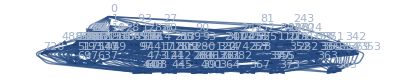

```mathematica
depgraph2=Graph[ allDependencies2,   ImageSize->800, VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding", VertexSize->Tiny,EdgeStyle->Arrowheads[0.001]]
```

```mathematica
Wave2[start_,n_]:=Select[Keys[newassocFour],GraphDistance[depgraph2,start,#]==n&]
```

```mathematica
WaveEnd2[end_,n_]:=Select[Keys[newassocFour],GraphDistance[depgraph2,#,end]==n&]
```

```mathematica
Map[newassocFour[#]["graph"]&,Wave2[0,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RelationsToEdges2[1]
```

{1→244,1→487,1→190,1→82,1→136,1→28,1→10,1→22,1→16,1→4,0→1,0→2}

```mathematica
Take[ret,5]
```

{x0==x243+x486,x0==x162+x81,x0==x27+x54,x0==x18+x9,x0==x3+x6}

```mathematica
{x0,x1,x9,x27,x243,x36,x244,x13,x109,x273,x333,x94,x112,x336,x354,x283,x361,x364}//Length
```

18

```mathematica
rep={x0->b0,
x1->b1,x9->b2,x27->b3,x243->b4,
x22->b5,x81->b6,
x244->b7,x36->b8,
x109->b9,x13->b10,x333->b11,x273->b12,
x84->b13,
x364->b14,

x10->b15,
x108->b16
}
```

{x0→b0,x1→b1,x9→b2,x27→b3,x243→b4,x22→b5,x81→b6,x244→b7,x36→b8,x109→b9,x13→b10,x333→b11,x273→b12,x84→b13,x364→b14,x10→b15,x108→b16}

```mathematica
retrep=ret/.rep;
```

```mathematica
dd=Reduce[retrep,{b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16}];
```

```mathematica
TableForm[Table[dd[[k]],{k,Length[dd]}]]
```

x91==x94+x97
x90==x93+x97
x82==x85+x97
x666==x697+x728
x606==x607+x608
x577==x607+x637
x576==x607+x608+x637
x546==x637+x728
x54==x63+x72
x517==x607+x697
x516==x607+x608+x697
x49==x697-x72+x728+x85-x94
x488==x608+x728
x487==x607+x637+x697
x486==x607+x608+x637+x697+x728
x45==x697-x72+x728+x85+x87-x94-x97
x448==x6-x728-x87
x442==x445+x6-x728-x87
x417==x445+x473
x414==x445+x473+x6-x728-x87
x400==x72-x728
x40==x445+x473-x63+x637+x94
x4==x445+x697+x85
x391==-x473+x63-x637
x39==x445+x473-x63+x637+x93
x382==-x473+x63-x637+x72-x728
x377==x87-x97
x373==-x72+x728+x85-x94
x37==x445+x473+x6-x63-x728-x87+x94+x97
x369==-x72+x728+x85+x87-x94-x97
x367==-x637+x97
x365==-x608+x93-x94
x363==x473-x607-x608-x63+x637+x93
x361==x473-x607-x63+x94+x97
x360==x473-x607-x608-x63+x93+x97
x357==-x637+x87
x355==x473-x607-x63+x637-x72+x728+x85
x354==x473-x607-x608-x63+x637-x72+x728+x85+x93-x94
x353==-x608+x87+x93-x94-x97
x352==x473-x607-x63-x72+x728+x85+x97
x351==x473-x607-x608-x63-x72+x728+x85+x87+x93-x94
x346==x85-x94
x342==x85+x87-x94-x97
x337==-x607+x94
x336==-x607-x608+x93
x334==-x607-x637+x94+x97
x328==-x607+x85
x327==-x607-x608+x85+x93-x94
x325==-x607-x637+x85+x97
x324==-x607-x608-x637+x85+x87+x93-x94
x31==x445+x473-x63+x637+x697-x72+x728+x85
x309==x63-x637
x300==x63-x637+x72-x728
x30==x445+x473-x63+x637+x697-x72+x728+x85+x93-x94
x3==x445+x473+x697+x85+x93-x94
x286==x6-x637-x728-x87+x97
x283==x445+x473-x607-x63+x637+x94
x282==x445+x473-x607-x608-x63+x637+x93
x280==x445+x473+x6-x607-x63-x728-x87+x94+x97
x28==x445+x473+x6-x63+x697-x72+x85-x87+x97
x279==x445+x473+x6-x607-x608-x63-x728-x87+x93+x97
x276==x6-x637-x728
x274==x445+x473-x607-x63+x637-x72+x728+x85
x271==x445+x473+x6-x607-x63-x72+x85-x87+x97
x270==x445+x473+x6-x607-x608-x63-x72+x85+x93-x94
x26==x728+x87-x97
x257==x473-x608+x93-x94
x256==x445-x607+x94
x255==x445+x473-x607-x608+x93
x253==x445+x6-x607-x637-x728-x87+x94+x97
x252==x445+x473+x6-x607-x608-x637-x728-x87+x93+x97
x247==x445-x607+x85
x246==x445+x473-x607-x608+x85+x93-x94
x245==x473-x608+x87+x93-x94-x97
x218==x473+x728
x2==x473+x728+x87+x93-x94-x97
x193==x445+x697
x190==x445+x6+x697-x728-x87
x18==x697+x728+x85+x87-x94-x97
x168==x6-x87
x165==x445+x473+x697
x162==x445+x473+x6+x697-x87
x16==x6-x728-x87+x97
x145==-x473+x63
x14==x473+x93-x94
x136==-x473+x63+x72-x728
x122==x93-x94
x121==x473-x63+x637+x94
x120==x473-x63+x637+x93
x12==x445+x473+x93
x118==x473-x63+x94+x97
x117==x473-x63+x93+x97
x112==x473-x63+x637-x72+x728+x85
x111==x473-x63+x637-x72+x728+x85+x93-x94
x110==x87+x93-x94-x97
b0==x445+x473+x6+x697+x85+x93-x94
b1==x445+x6+x697-x728+x85-x87+x97
b2==x445+x473+x6-x728-x87+x93+x97
b3==x445+x473+x6-x63+x697-x72+x85+x93-x94
b4==x445+x473+x6-x607-x608-x637-x728+x85+x93-x94
b5==x697+x85-x94
b6==x85+x87+x93-x94
b7==x445+x6-x607-x637-x728+x85-x87+x97
b8==x445+x473+x6-x63-x728-x87+x93+x97
b9==x473-x63-x72+x728+x85+x97
b10==x445+x94
b11==-x607-x608-x637+x93+x97
b12==x445+x473-x607-x608-x63+x637-x72+x728+x85+x93-x94
b13==x85+x93-x94
b14==x473-x607-x63+x637+x94
b15==x445+x6-x728-x87+x94+x97
b16==x473-x63-x72+x728+x85+x87+x93-x94

```mathematica
Total[Table[Fibonacci[k],{k,50}]]
```

32951280098

```mathematica
newassocFour[364]["graph"]
```

-Graphics-